```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar\\"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar\2017-10-12_B0_for_mirror\scope_0_14_2.csv

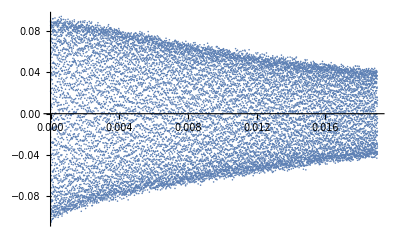

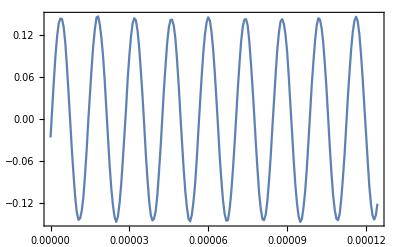

```mathematica
fn=StringJoin[curDir,"\\2017-10-12_B0_for_mirror\\","scope_0_14_2.csv"]
dat=Import[fn];
stab=Select[dat,#[[1]]>0&&#[[1]]<0.05&];
ListPlot[stab]
```

FittedModel[-0.00107081+ⅇ^(6.3107×10^-14 t) (0.0243334 Cos[223528. t]+0.0807735 Sin[223528. t])]

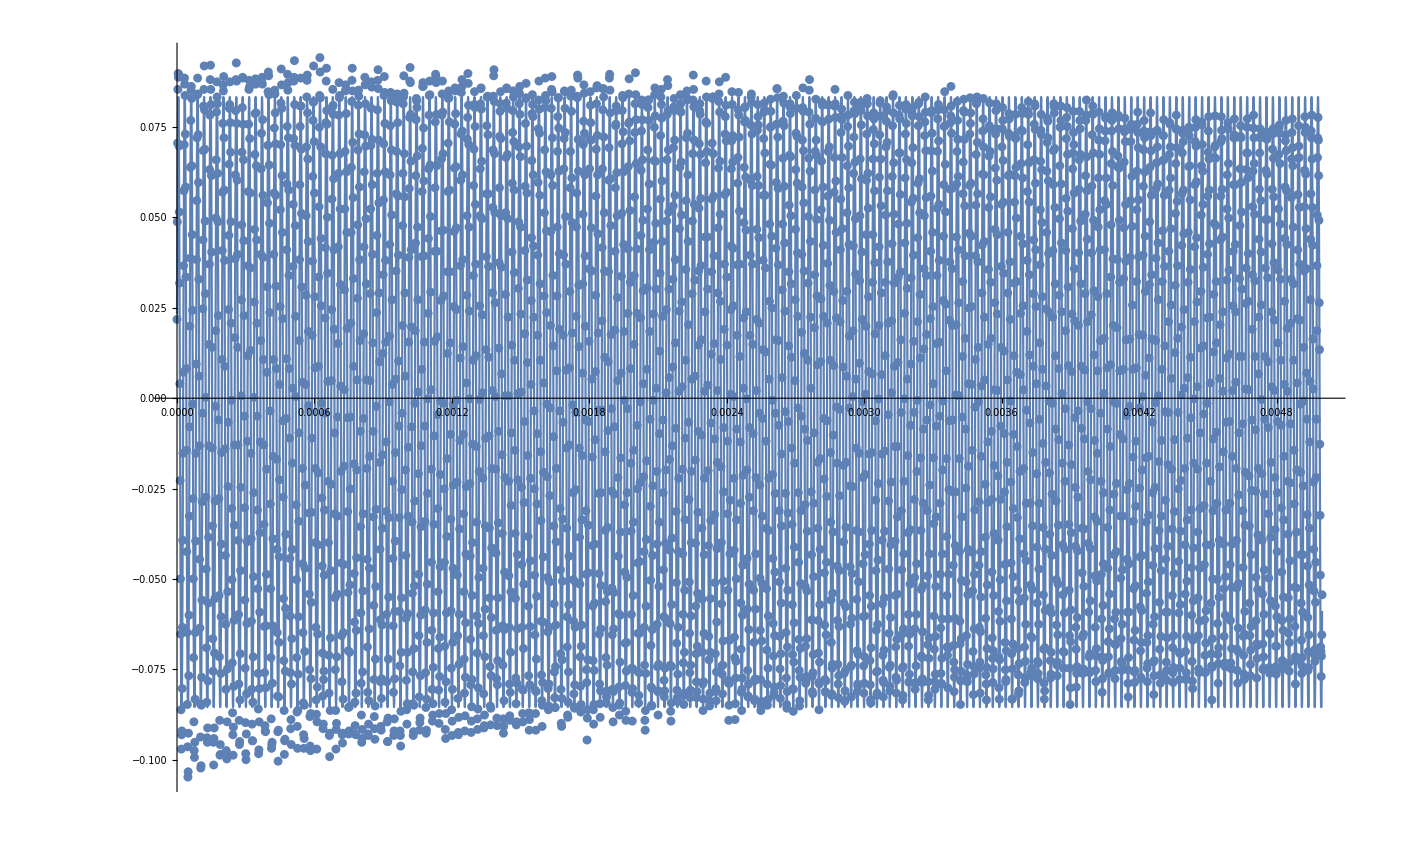

| Estimate | Standard Error | Confidence Interval
f | 35575.6 | 0.146214 | {35575.3,35575.9}
As | 0.0807735 | 0.00012498 | {0.0805284,0.0810185}
Ac | 0.0243334 | 0.000216476 | {0.0239089,0.0247578}
c | -0.00107081 | 0.0000790312 | {-0.00122575,-0.000915861}
tau | -1.58461×10^13 | 7.75365×10^-32 | {-1.58461×10^13,-1.58461×10^13}

```mathematica
fitdat=stab[[1;;4000]];
reg=NonlinearModelFit[fitdat,(As Sin[2. Pi f t]+Ac Cos[2. Pi f t])Exp[-t/tau]+c,{{f,71278/2},{As,0.1},{Ac,0.1},{c,0},{tau,0.01}},t]
Show[
ListPlot[fitdat,Joined->False],
Plot[reg[t],{t,fitdat[[1,1]],fitdat[[-1,1]]},PlotPoints->1000]
]
reg["ParameterConfidenceIntervalTable"]
```

```mathematica
71.271/3.5332539
```

20.1715

```mathematica
dat[[1]]
```

{-0.005425,-0.0317992}